## Basis functions and coefficients of PDE

```mathematica
basisfunction[j_,x_,L_]:=√(2/L)*Sin[ Pi*j* x/L] 
dbasisfunction[j_,x_,L_]:=(√2 *j* π Cos[Pi*j* x/L])/L^(3/2)
A[t_,x_]:=1 (*Coefficients of PDE*)
b[t_,x_]:=Cos[x]
c[t_,x_]:=Sin[x]
f[t_,x_]:=1
g[x_]:=1
```

## Function to calculation coefficients λ_n of approximate solution u_n(t,x)=λ_n(t)*ϕ(x)

```mathematica
soln[A_,b_,c_,f_,g_,n_,L_,T_]:=Module[{Bn,fn,gn,lambdan,expBn,lambdaSol},
Bn[t_]:=Table[Integrate[A[t,x]*dbasisfunction[i,x,L]*dbasisfunction[j,x,L]+b[t,x]*dbasisfunction[i,x,L]*basisfunction[j,x,L]+c[t,x]*basisfunction[i,x,L]*basisfunction[j,x,L],{x,0,L}],{i,1,n},{j,1,n}];
fn[t_]:=Table[Integrate[basisfunction[j,x,L]*f[t,x],{x,0,L}],{j,1,n}];
gn=Table[Integrate[basisfunction[j,x,L]*g[x],{x,0,L}],{j,1,n}];
(*Now use the result in the outer integral over s*)
lambdaSol=NDSolve[{D[lambdan[t],t]+Bn[t].lambdan[t]==fn[t],lambdan[0]==gn},lambdan,{t,0,T}];
lambdan/. lambdaSol[[1]]
]
```

## Plotting approximation

```mathematica
L=2π;n=20;
lambdan=soln[A,b,c,f,g,n,L,1];
u20[t_,x_]:=Sum[lambdan[t][[i]]*basisfunction[i,x,L],{i,1,n}];
```

```mathematica
p20=Plot3D[u20[t,x],{t,0,1},{x,0,2 Pi},PlotRange->All,AxesLabel->{Style["t",18],Style["x",18],Style["u_20(t,x)",18]},ColorFunction->"LightTemperatureMap"]
```

-Graphics3D-

```mathematica
lambda3=soln[A,b,c,f,g,3,L,1];
u3[t_,x_]:=Sum[lambda3[t][[i]]*basisfunction[i,x,L],{i,1,2}];
p3=Plot3D[u3[t,x],{t,0,1},{x,0,2 Pi},PlotRange->All,AxesLabel->{Style["t",18],Style["x",18],Style["u_3(t,x)",18]},ColorFunction->"LightTemperatureMap"]
```

-Graphics3D-

## Solution obtained with Mathematica

```mathematica
solMathematica=NDSolve[{D[u[t,x],t]-A[t,x] D[u[t,x],{x,2}]+b[t,x] D[u[t,x],x]+c[t,x] u[t,x]==f[t,x],u[0,x]==g[x],u[t,0]==0,u[t,L]==0 },u,{t,0,10},{x,0,L}];//Quiet


pmath=Plot3D[Evaluate[u[t,x]/. solMathematica],{t,0,1},{x,0,L},PlotRange->All,AxesLabel->{"t","x","u(t, x)"},PlotLegends->Automatic]
```

-Graphics3D-

## Approximation of g=1 with basis functions in H_0^1(U)

```mathematica
L=2 Pi; (*domain length U=(0,2π)*)
basisfunction[n_,x_]:=√(2/L)*Sin[n Pi x/L] (*orthonormal eigenfunctions of the Laplacian in H_0^1(U)*)
g[x_]:=1 (*Source*)
basisCoefficient[n_]:=Integrate[g[x] basisfunction[n,x],{x,0,L}](*basis coefficients*)
approximationFunction[N_,x_]:=Sum[basisCoefficient[n] basisfunction[n,x],{n,1,N}]
```

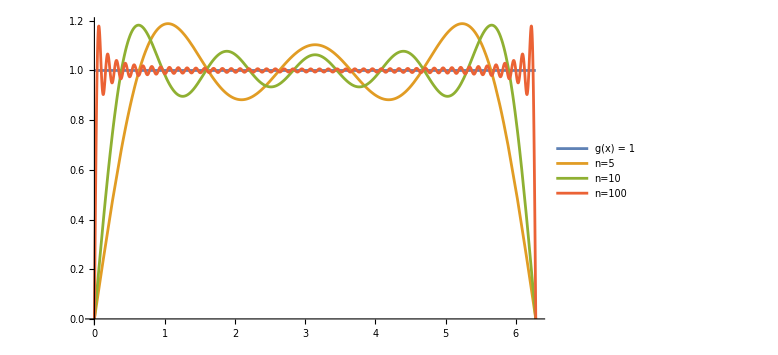

```mathematica
a5=approximationFunction[5,x];
a10=approximationFunction[10,x];
a100=approximationFunction[100,x];
papproxg=Plot[{g[x],a5,a10,a100},{x,0,2π},PlotRange->Full,PlotLegends->{"g(x) = 1","n=5","n=10","n=100"},ImageSize->Large]
```

## Comparing to case with exact solution

```mathematica
solexact[t_,x_]:=t*(x-1)*x
A[t_,x_]:=1 (*Coefficients of PDE*)
b[t_,x_]:=1
c[t_,x_]:=1
f[t_,x_]:=(-1+x) x+t (-3+x+x^2)
g[x_]:=0
D[solexact[t,x],t]-D[A[t,x]*D[solexact[t,x],x],x]+b[t,x]*D[solexact[t,x],{x,1}]+c[t,x]*solexact[t,x];//FullSimplify
{D[solexact[t,x],t]-A[t,x] D[solexact[t,x],{x,2}]+b[t,x] D[solexact[t,x],x]+c[t,x] solexact[t,x]==f[t,x],solexact[0,x]==g[x],solexact[t,0]==0,solexact[t,1]==0}//FullSimplify(*Checking equations hold for exact solution*)
```

{True,True,True,True}

```mathematica
L=1;n=20;
lambdan=soln[A,b,c,f,g,n,L,1];
u20[t_,x_]:=Sum[lambdan[t][[i]]*basisfunction[i,x,L],{i,1,n}];
```

```mathematica
q20=Plot3D[u20[t,x],{t,0,1},{x,0,1},PlotRange->All,AxesLabel->{Style["t",18],Style["x",18],Style["u_20(t,x)",18]},ColorFunction->"LightTemperatureMap"]
```

-Graphics3D-

```mathematica
qexact=Plot3D[solexact[t,x],{t,0,1},{x,0,L},AxesLabel->{Style["t",18],Style["x",18],Style["u(t,x)",18]},ColorFunction->"LightTemperatureMap"]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\liaml\\Documentos\\LiamLlamazares.github.io\\assets\\img\\Figures\\Galerkin_n_20.svg",p20];
Export["C:\\Users\\liaml\\Documentos\\LiamLlamazares.github.io\\assets\\img\\Figures\\Galerkin_n_3.svg",p3];
Export["C:\\Users\\liaml\\Documentos\\LiamLlamazares.github.io\\assets\\img\\Figures\\approx_boundary_l2.svg",papproxg];
Export["C:\\Users\\liaml\\Documentos\\LiamLlamazares.github.io\\assets\\img\\Figures\\Galerkin_n_20_2.svg",q20];
Export["C:\\Users\\liaml\\Documentos\\LiamLlamazares.github.io\\assets\\img\\Figures\\Galerkin_exact.svg",qexact];
```